# Pandemia - model SIR

## Wstęp teoretyczny

S: liczba zdrowych, zdolnych do bycia zakażonymi.
I: liczba zainfekowanych
R: liczba zmarłych/ wyleczonych/ usuniętych z populacji. 
Każdy członek S może zostać zarażony z prawdpodobieństwem β przez swojego sąsiada.
Każdy zainfekowany I, może przejść do R zgodnie z prawdopodobieństwem γ.

## Technika

Symulacja będzie przebiegać na kwadratowej tablicy o wymiarze N. Kolorem zielonym będą zaznaczeni S, czerwonym I, i niebieskim R.
Symulacje będą się odbywać zgodnie z dwoma alternatywnymi algorytmami: synchronicznym i asynchroniczny.
Przeprowadzone zostaną dwie symulacje: dla modelu SIR i modelu SIS.

## Program

### Zapis do pliku

```mathematica
SetDirectory[NotebookDirectory[]<>"/dane/"]
```

/home/jacek/MEGAsync/uczelnia/5-semestr/lab/epidemia/dane

```mathematica
DumpSave["danePandemiaSynSIR.mx",{daneSynAll}]
```

{{{1},{1},{1},{1},{1}}}
 |  |  |  |

```mathematica
DumpSave["danePandemiaSynSIS.mx",{daneSisSynAll}]
```

DumpSave::noopen: Cannot open dane/danePandemiaSynSIS.mx.

DumpSave[dane/danePandemiaSynSIS.mx,{daneSisSynAll}]

```mathematica
DumpSave["daneBetaST.mx",{pomiary}];
```

### Wczytywanie danych

```mathematica
SetDirectory["dane/"]
```

/home/jacek/MEGAsync/uczelnia/5-semestr/lab/epidemia/dane

```mathematica
<<danePandemiaSynSIR.mx
```

```mathematica
<<danePandemiaSynSIS.mx
```

## SIR

## Chroniczny

Funkcja ma przyjąć tablicę NxN, której elementy mogą przyjmować trzy rodzaje wartość S, I i R, i narysować diagram. Użyjemy funkcji MatrixPlot

```mathematica
wyk[mat_]:=MatrixPlot[mat,ColorRules->{s->Green,i->Red,r->Blue},PlotLegends->Automatic]
```

Zwraca daną komórkę o ile jej adres nie przekracza zakresu wymiarów tablicy.

```mathematica
takeElement[bTab_,x_,y_]:=
If[x<1∨x>n∨y<1∨y>n,Null,bTab[[x,y]]]
```

Zwraca liczbę zakażonych sąsiadów.

```mathematica
ileSomsiadow[bTab_,x_,y_]:=
Count[{
takeElement[bTab,x-1,y-1],
takeElement[bTab,x,y-1],
takeElement[bTab,x+1,y-1],
takeElement[bTab,x-1,y],
takeElement[bTab,x+1,y],
takeElement[bTab,x-1,y+1],
takeElement[bTab,x,y+1],
takeElement[bTab,x+1,y+1]
},i]
```

#### Wykres uśredniony S̄(t), Ī(t), R̄(t)

```mathematica
ClearAll[wykresMeanSIR,wykresMeanSIS];
wykresMeanSIR[tablica_,nTur_,nSym_,tytul_:"SIR Synchroniczny"]:=
DiscretePlot[{
Mean@Table[Count[tablica[[ns,x]],s,2],{ns,nSym}],
Mean@Table[Count[tablica[[ns,x]],i,2],{ns,nSym}],
Mean@Table[Count[tablica[[ns,x]],r,2],{ns,nSym}]}
,{x,1,nTur},PlotTheme->"Scientific",PlotLabel->tytul,FrameLabel->{"czas","ilość"},Filling->None,PlotLegends->{"S","I","R"}];
wykresMeanSIS[tablica_,nTur_,nSym_,tytul_:"SIS Synchroniczny"]:=
DiscretePlot[{
Mean@Table[Count[tablica[[ns,x]],s,2],{ns,nSym}],
Mean@Table[Count[tablica[[ns,x]],i,2],{ns,nSym}]}
,{x,1,nTur},PlotTheme->"Scientific",PlotLabel->tytul,FrameLabel->{"czas","ilość"},Filling->None,PlotLegends->{"S","I"}];
```

#### Główna pętla programu

Model Synchroniczny - 
ZMIANA!!! Początkowy procent chorych σ.

Inicjalizacja. Parametry symulacji

```mathematica
β=0.05;
γ=0.03;
n=100;
σ=0.01;
nTur=250;
nSym=5;
```

```mathematica
ClearAll[daneSyn]
```

Główna pętla programu. Podczas iteracji może wystąpić zdarzenie przejścia z S→I lub I→R. Prawdopodobieństwo przejścia I→R wynosi γ. Prawdopodobieństwo zakażenia się od jednego ze swoich r chorych sąsiadów (znajdujących się w stanie I) wynosi 1-β^r

Generowanie nowych danych dla modelu SIR wg algorytmu synchronicznego

```mathematica
ClearAll[daneSynAll];
daneSynAll={};
Do[
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n];
daneSyn={tab};
curTab=tab;
Do[
{
oldTab=curTab;
Do[{liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤γ∧oldTab[[x,y]]==i,curTab[[x,y]]=r,]
}
,{x,1,n},{y,1,n}];
AppendTo[daneSyn,curTab];}
,nTur];
AppendTo[daneSynAll,daneSyn];
,nSym]
```

Animacja wykorzystująca zdefiniowaną wcześniej funkcję wyk[].

Animacja

```mathematica
Animate[wyk[daneSynAll[[ns,u]]],{u,1,nTur,1},{ns,1,nSym,1},AnimationRunning->False]
```

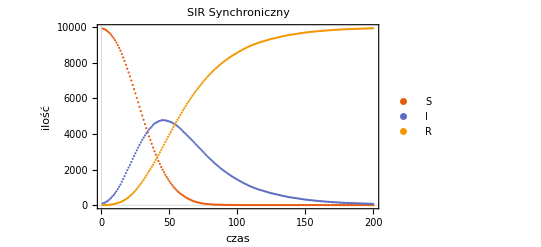

```mathematica
wykresMeanSIR[daneSynAll,nTur,nSym]
```

```mathematica
daneSynAll[[1,nTur]]
```

{{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,s,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,s,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,s,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,s,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,s,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{s,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{s,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,i,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r},{r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r}}

### SIS

#### Chroniczny

Wykorzystamy model SIS: β - oznacza p. S→ I, α - p. I→ S czyli wyzdrowienia

Inicjalizacja

```mathematica
β=0.05;
α=0.02;
n=100;
σ=0.01;
nTur=60;
nSym=6;
```

Pętla

```mathematica
daneSisSynAll={};
Do[
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n];
daneSisSyn={tab};
curTab=tab;
Do[
{
oldTab=curTab;
Do[{ liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤α∧curTab[[x,y]]==i,curTab[[x,y]]=s,]
}
,{x,1,n},{y,1,n}];
AppendTo[daneSisSyn,curTab]}
,nTur]
AppendTo[daneSisSynAll,daneSisSyn];
,nSym]
```

Animacja

```mathematica
Animate[wyk[daneSisSynAll[[ns,t]]],{ns,1,nSym,1},{t,1,nTur,1},AnimationRunning->False]
```

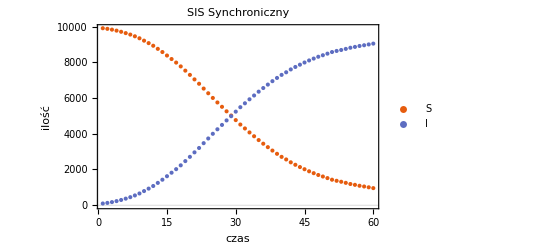

```mathematica
wykresMeanSIS[daneSisSynAll,nTur,nSym]
```

## Model asynchroniczny

Pętla będzie iterowana tak samo jak w modelu chronicznym. Inaczej będziemy zapisywać wartości do zmiennej zbierającej dane eksperymentu. Będzie ona aktualizowana po sprawdzeniu każdego elementu macierzy.

#### Model SIR

Inicjalizacja

```mathematica
β=0.05;
γ=0.03;
σ=0.01;
n=30;
nTur=10;
nSym=6;
```

Pętla programu

```mathematica
daneASirAll={};
Do[
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n];
daneASir={tab};
curTab=tab;
Do[
{
oldTab=curTab;
Do[{liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤γ∧oldTab[[x,y]]==i,curTab[[x,y]]=r,],
AppendTo[daneASir,curTab];
}
,{x,1,n},{y,1,n}];
}
,nTur];
AppendTo[daneASirAll,daneASir];
,nSym]
```

Animacja

```mathematica
Animate[wyk[daneASirAll[[1,u]]],{u,1,nTur*n^2,1},AnimationRunning->False]
```

```mathematica
daneASirAll[[1,u]]
```

Part::pkspec1: The expression u cannot be used as a part specification.

$Aborted[]

Part::partd: Part specification tablica⟦1,1⟧ is longer than depth of object.

tablica⟦1,1⟧

```mathematica
DiscretePlot[{
Mean@Table[Count[tablica[[ns,x]],s,2],{ns,nSym}],
Mean@Table[Count[tablica[[ns,x]],i,2],{ns,nSym}],
Mean@Table[Count[tablica[[ns,x]],r,2],{ns,nSym}]}
,{x,1,nTur},PlotTheme->"Scientific",PlotLabel->tytul,FrameLabel->{"czas","ilość"},Filling->None,PlotLegends->{"S","I","R"}];
```

#### SIS

Inicjalizacja

```mathematica
β=0.05;
α=0.02;
n=50;
σ=0.01;
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n];
nTur=5;
```

Pętla

```mathematica
daneASIS={tab};
curTab=tab;
Do[
{
oldTab=curTab;
Do[{ liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤α∧curTab[[x,y]]==i,curTab[[x,y]]=s,],
AppendTo[daneASIS,curTab]
}
,{x,1,n},{y,1,n}];
}
,nTur]
```

Animacja

```mathematica
Animate[wyk[daneASIS[[u]]],{u,1,nTur*n^2,1},AnimationRunning->False]
```

## Zależność przebiegu symulacji od parametrów β i γ

Sprawdzimy w jaki sposób zmieniają się przebiegi funkcji S(t_k)(β),I(t_k)(β),R(t_k)(β) i S(t_k)(γ),I(t_k)(γ),R(t_k)(γ), gdzie t_k - końcowa chwila symulacji.

## Zależność od β

symulacji

```mathematica
γ=0.03;
n=100;
σ=0.01;
nTur=250;
begPar=0.01;
endPar=0.5;
dPar=0.01;
```

```mathematica
ClearAll[daneSyn]
```

Główna pętla programu. Podczas iteracji może wystąpić zdarzenie przejścia z S→I lub I→R. Prawdopodobieństwo przejścia I→R wynosi γ. Prawdopodobieństwo zakażenia się od jednego ze swoich r chorych sąsiadów (znajdujących się w stanie I) wynosi 1-β^r

Generowanie nowych danych dla modelu SIR wg algorytmu synchronicznego

```mathematica
pomiary=Table[{0,0,0,0},{i,IntegerPart[(endPar-begPar)/dPar+1]}];
For[β=begPar,β≤endPar,β+=dPar,
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n]; (* Pierwsza tablica *)
daneSyn={tab};
curTab=tab;
iS=IntegerPart[(β-begPar)/dPar +1];(* Numer pomiaru β*)
pomiary[[iS,1]]=β;
pomiary[[iS,2]]=γ;
Do[
{
oldTab=curTab;
Do[{liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤γ∧oldTab[[x,y]]==i,curTab[[x,y]]=r,]
}
,{x,1,n},{y,1,n}];
AppendTo[daneSyn,curTab];}
,nTur];
pomiary[[iS,3]]=Count[daneSyn[[nTur]],s,2];
pomiary[[iS,4]]=Count[daneSyn[[nTur]],r,2];
]
```

```mathematica
pomiary
```

{{0.01,0.03,6846,2865},{0.02,0.03,314,9495},{0.03,0.03,72,9893},{0.04,0.03,18,9965},{0.05,0.03,8,9972},{0.06,0.03,4,9982},{0.07,0.03,4,9982},{0.08,0.03,0,9994},{0.09,0.03,0,9991},{0.1,0.03,0,9995},{0.12,0.03,0,9996},{0.13,0.03,0,9994},{0.14,0.03,0,9992},{0.15,0.03,0,9994},{0,0,0,0},{0.16,0.03,0,9990},{0.17,0.03,0,9994},{0.18,0.03,0,9989},{0.19,0.03,0,9996},{0.2,0.03,0,9996},{0.21,0.03,0,9989},{0.22,0.03,0,9995},{0.23,0.03,0,9994},{0.24,0.03,0,9993},{0.25,0.03,0,9992},{0.26,0.03,0,9993},{0.27,0.03,0,9994},{0.28,0.03,0,9991},{0.29,0.03,0,9990},{0.3,0.03,0,9997},{0.31,0.03,0,9993},{0.32,0.03,0,9994},{0.33,0.03,0,9996},{0.34,0.03,0,9990},{0.35,0.03,0,9989},{0.36,0.03,0,9996},{0.37,0.03,0,9996},{0.38,0.03,0,9994},{0.39,0.03,0,9992},{0.4,0.03,0,9994},{0.41,0.03,0,9994},{0.42,0.03,0,9990},{0.43,0.03,0,9995},{0.44,0.03,0,9996},{0.45,0.03,0,9996},{0.46,0.03,0,9994},{0.47,0.03,0,9995},{0.48,0.03,0,9992},{0.49,0.03,0,9990},{0.5,0.03,0,9996}}

```mathematica
sTvsβ={pomiaryᵀ[[1]]}
```

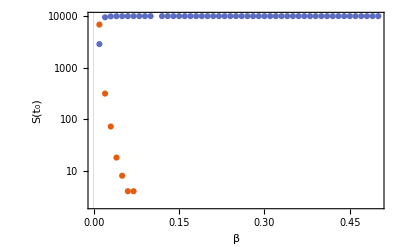

```mathematica
ListLogPlot[{{pomiaryᵀ[[1]],pomiaryᵀ[[3]]}ᵀ,{pomiaryᵀ[[1]],pomiaryᵀ[[4]]}ᵀ}
,PlotTheme->"Scientific",FrameLabel->{"β","S(t_0)"}]
```

```mathematica
pomiary=Table[{0,0,0,0},{i,IntegerPart[(endPar-begPar)/dPar+1]}];
For[β=begPar,β≤endPar,β+=dPar,
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n]; (* Pierwsza tablica *)
daneSyn={tab};
curTab=tab;
iS=IntegerPart[(β-begPar)/dPar +1];(* Numer pomiaru β*)
pomiary[[iS,1]]=β;
pomiary[[iS,2]]=γ;
Do[
{
oldTab=curTab;
Do[{liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤γ∧oldTab[[x,y]]==i,curTab[[x,y]]=r,]
}
,{x,1,n},{y,1,n}];
AppendTo[daneSyn,curTab];}
,nTur];
pomiary[[iS,3]]=Count[daneSyn[[nTur]],s,2];
pomiary[[iS,4]]=Count[daneSyn[[nTur]],r,2];
]
```

## Inny algorytm

```mathematica
γ=0.03;
n=100;
σ=0.02;
nTur=200;
begPar=0.01;
endPar=0.02;
dPar=0.01;
```

```mathematica
nSym=IntegerPart[(endPar-begPar)/dPar+1];
nSasiad=Table[0,{i,n},{j,n}];
pomiary=Table[{0,0,0,0},{i,nSym}];
For[β=begPar,β≤endPar,β+=dPar,
tab=Table[Table[RandomChoice[{1-σ,σ}->{s,i}],n],n]; (* Pierwsza tablica *)
	For[x=1,x≤Dimensions[tab][[1]],x++,For[y=1,y≤Dimensions[tab][[2]],y++,
	If[tab[[x,y]]==i,
{
If[x<n∧y<n,nSasiad[[x+1,y+1]]+=1,],
If[x<n,nSasiad[[x+1,y]]+=1,],
If[x<n∧y>1,nSasiad[[x+1,y-1]]+=1,],
If[y>1n,nSasiad[[x,y+1]]+=1,],
If[y<n,nSasiad[[x,y-1]]+=1,],
If[x>1∧y<n,nSasiad[[x-1,y+1]]+=1,],
If[x>1,nSasiad[[x-1,y]]+=1,],
If[x>1∧y>1,nSasiad[[x-1,y-1]]+=1,]}
,]
]];
daneSyn={tab};
curTab=tab;
iS=IntegerPart[(β-begPar)/dPar +1];(* Numer pomiaru β*)
pomiary[[iS,1]]=β;
pomiary[[iS,2]]=γ;
Do[
{oldTab=curTab;
Do[
(*{liczbaSomsiadow=ileSomsiadow[oldTab,x,y],
If[liczbaSomsiadow>0∧RandomReal[]≤1-(1-β)^liczbaSomsiadow∧curTab[[x,y]]==s,curTab[[x,y]]=i,],
If[RandomReal[]≤γ∧oldTab[[x,y]]==i,curTab[[x,y]]=r,]
}
*){cnS=nSasiad[[x,y]],
Switch[curTab[[x,y]],
s,If[cnS>0∧RandomReal[]≤1-(1-β)^cnS,
{curTab[[x,y]]=i,
If[x<n∧y<n,nSasiad[[x+1,y+1]]+=1,],
If[x<n,nSasiad[[x+1,y]]+=1,],
If[x<n∧y>1,nSasiad[[x+1,y-1]]+=1,],
If[y>1n,nSasiad[[x,y+1]]+=1,],
If[y<n,nSasiad[[x,y-1]]+=1,],
If[x>1∧y<n,nSasiad[[x-1,y+1]]+=1,],
If[x>1,nSasiad[[x-1,y]]+=1,],
If[x>1∧y>1,nSasiad[[x-1,y-1]]+=1,]}
,],
i,If[RandomReal[]≤γ∧oldTab[[x,y]]==i,
{curTab[[x,y]]=r,
If[x<n∧y<n,nSasiad[[x+1,y+1]]-=1,],
If[x<n,nSasiad[[x+1,y]]-=1,],
If[x<n∧y>1,nSasiad[[x+1,y-1]]-=1,],
If[y>1n,nSasiad[[x,y+1]]-=1,],
If[y<n,nSasiad[[x,y-1]]-=1,],
If[x>1∧y<n,nSasiad[[x-1,y+1]]-=1,],
If[x>1,nSasiad[[x-1,y]]-=1,],
If[x>1∧y>1,nSasiad[[x-1,y-1]]-=1,]}
,]
]}

,{x,1,n},{y,1,n}];
AppendTo[daneSyn,curTab];}
,nTur];
pomiary[[iS,3]]=Count[daneSyn[[nTur]],s,2];
pomiary[[iS,4]]=Count[daneSyn[[nTur]],r,2];
]
```

```mathematica
pomiary
```

{{0.01,0.03,9791,209},{0.02,0.03,9803,196}}

```mathematica
Manipulate[wyk[daneSyn[[q]]],{q,1,nTur,1}]
```

```mathematica
Dimensions@daneSyn
```

{4,5,5}